```mathematica
(** chapter 10**)
```

```mathematica
(**Ex-01**)
```

```mathematica
d[x1_,y1_,x2_,y2_]=√((x2-x1)^2+(y2-y1)^2);
d[2,3,8,11]
```

10

```mathematica
(**Ex- 05)
```

```mathematica
f[x_,y_]=√((x-3)^2+(y-4)^2);
f[5,-2]
```

2 √10

```mathematica
(**Ex-07**)
```

```mathematica
s=(a+b+c)/2;
A[a_,b_,c_]=√(s(s-a)(s-b)(s-c));
A[3,4,5]
```

6

```mathematica
A[5,9,12]
```

4 √26

```mathematica
A[5,7,9]
```

(21 √11)/4

```mathematica
(**Ex- 15**)
```

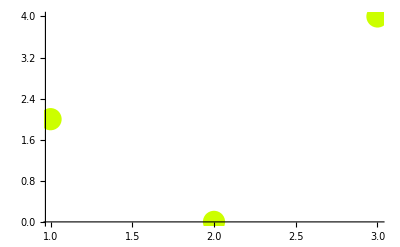

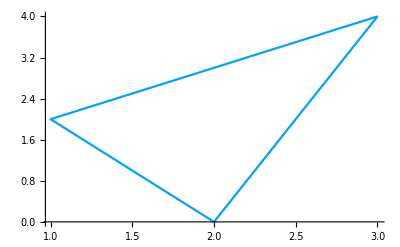

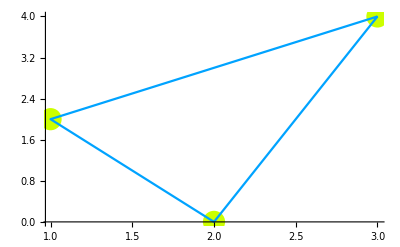

```mathematica
u={3,4};
v={1,2};
w={2,0};
pt1={u,v,w};
pt2={u,v,w,u};
p1=ListPlot[pt1,PlotStyle->{Hue[0.2],PointSize[0.04]}]
p2=ListPlot[pt2,PlotStyle->{Hue[0.56],PointSize[0.04]},Joined->True]
Show[p1,p2]
```

```mathematica
(**Ex-32**)
```

```mathematica
fg=x^2-5x*y+4 y^2+x+2y-2==0;
a=1;b=4;h=-5/2;g=1/2;f=1;c=-2;
d=a*b*c+2f*g*h-a*f^2-b*g^2-c*h^2
eq1=D[fg,x];
eq2=D[fg,y];
Solve[{eq1,eq2},{x,y}]
Alfa=ArcTan[(√(h^2-a*b))/(a+b)]
```

0

{{x→2,y→1}}

ArcTan[3/10]

```mathematica
Exit[]
```

```mathematica
(**Ex-41**)
```

```mathematica
intersec=NSolve[{x^2+y^2+19x+4y-3==0,3x+4y==1},{x,y}]
m1=intersec[[1,2,2]]/intersec[[1,1,2]];
m2=intersec[[2,2,2]]/intersec[[2,1,2]];
Angle=ArcTan[Abs[(m1-m2)/(1+m1*m2)]]
```

{{x→-10.1225,y→7.84187},{x→0.122499,y→0.158125}}

1.5708

```mathematica
Angle==90 Degree
```

True